```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

```mathematica
SetDirectory@NotebookDirectory[];
omarker=Graphics[{Thickness[.2],Disk[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x)
colorsDefault=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Default",ListPlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
errorData=Import["../methodsCompare.csv"];
%//TableForm
```

| GEM | Cholesky
2 | 4.44089×10^-16 | 2.22045×10^-16
3 | 6.51331×10^-15 | 4.73695×10^-15
4 | -8.72953×10^-14 | -8.66862×10^-14
5 | 3.66843×10^-13 | -2.51807×10^-12
6 | 1.86702×10^-10 | -1.79028×10^-12
7 | 6.14563×10^-9 | 1.35239×10^-9
8 | -1.98952×10^-8 | -4.47141×10^-8
9 | -2.8791×10^-6 | -3.98235×10^-6
10 | -0.0000832348 | -0.000157734
11 | -0.00201529 | -0.00378353

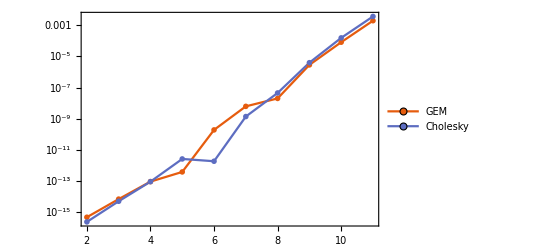

errorPlot.pdf

```mathematica
errorPlot=ListLogPlot[Abs/@{
errorData⟦2;;⟧⟦All,{1,2}⟧,errorData⟦2;;⟧⟦All,{1,3}⟧
},Joined->True,
PlotTheme->"Scientific",
PlotRangePadding->{{.5,.5},{3,3}},
PlotMarkers->{omarker,.03},
PlotLegends->{"GEM","Cholesky"}]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@errorPlot
```